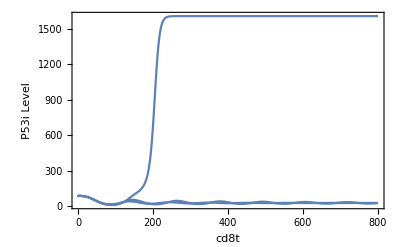

```mathematica
k1=1.3;
k2=0.28;
k4=3;
kp=10;
ke=1000;
μ=1.6;
a1=10^4.05;
Show@Table[
Module[{t,a,b},
sol = First[NDSolve[{
a'[t] == k1*a[t]*(1-a[t]/a1)-k2*a[t]*b[t]-a[t],a[t /; t ≤ 0] ==80,
b'[t] ==1+(b[t]*a[t-τ])/(kp+a[t-τ])-k4*(a[t]*b[t])/(ke+a[t])-μ*b[t],b[t /; t ≤ 0]  ==0.625},
{a,b}, {t,0,4000}]];
Plot[Evaluate[{a[t]} /. sol],{t,0,800},Frame->True,FrameLabel->{"cd8t","P53i Level"},PlotRange->All,PlotStyle->{PlotStyle->Black},BaseStyle->{FontWeight->"Plain",FontSize->18}]],{τ,{18,20,23}}]
```